# Лабораторная работа №8

### Загрузка данных

```mathematica
data=First[ Import["D:\\User\\Documents\\import_data_8.xlsx"]];
```

### Используем метод главных компонент, перейти от пространства исходных признаков (показателей) к факторному пространству главных компонент, объясняющих не менее 70% вариации исходных признаков.

```mathematica
data[[;;4,;;]]
```

{{0.9001,0.098,10.1254,1.08277×10^8,1.1161×10^9,1.1026×10^9,7.9787×10^7,7.1922×10^7,0.0733,0.0593},{-0.3733,2.0889,1.567,1.16375×10^8,1.38778×10^8,3.76678×10^8,3.52069×10^8,9.9573×10^7,0.0464,0.0996},{0.1258,2.5412,1.5647,3.07856×10^8,2.91719×10^8,1.08201×10^9,2.07403×10^8,1.68574×10^8,0.0095,0.1525},{0.0475,4.7775,1.0498,2.1153×10^8,5.4584×10^7,2.7382×10^8,4.1598×10^7,8.0602×10^7,0.1778,0.0567}}

```mathematica
standartData=Standardize[data];
```

```mathematica
n=Length[data];
k=Length[data[[1]]];
```

```mathematica
A=Covariance[standartData];
A//MatrixForm
```

(1. | -0.013087 | 0.378093 | -0.0014704 | 0.295987 | 0.164178 | -0.209793 | 0.277688 | 0.331194 | 0.262433
-0.013087 | 1. | 0.0108594 | -0.288345 | 0.0298252 | -0.306607 | -0.101288 | 0.0464759 | 0.0596754 | 0.0444459
0.378093 | 0.0108594 | 1. | -0.150891 | 0.380507 | 0.0437357 | 0.105107 | 0.232521 | 0.130706 | 0.250334
-0.0014704 | -0.288345 | -0.150891 | 1. | -0.0326961 | 0.777012 | 0.025033 | 0.0516031 | -0.154897 | 0.000148568
0.295987 | 0.0298252 | 0.380507 | -0.0326961 | 1. | 0.362913 | 0.449786 | 0.768436 | 0.280296 | 0.733995
0.164178 | -0.306607 | 0.0437357 | 0.777012 | 0.362913 | 1. | 0.153217 | 0.328192 | -0.163193 | 0.217349
-0.209793 | -0.101288 | 0.105107 | 0.025033 | 0.449786 | 0.153217 | 1. | 0.336952 | -0.106435 | 0.386704
0.277688 | 0.0464759 | 0.232521 | 0.0516031 | 0.768436 | 0.328192 | 0.336952 | 1. | 0.469549 | 0.93362
0.331194 | 0.0596754 | 0.130706 | -0.154897 | 0.280296 | -0.163193 | -0.106435 | 0.469549 | 1. | 0.533534
0.262433 | 0.0444459 | 0.250334 | 0.000148568 | 0.733995 | 0.217349 | 0.386704 | 0.93362 | 0.533534 | 1.)

```mathematica
ownLambda =Eigenvalues[A];
ownVectors=Eigenvectors[A];
```

```mathematica
Table[Sum[ownLambda[[i]]/k,{i,1,j}],{j,1,k}]
```

{0.344896,0.549858,0.686536,0.789736,0.874844,0.922252,0.960341,0.984715,0.994927,1.}

Заметим, что первые 4 признаков объясняют 78% исходных признаков, оставим их в качестве главных компонент.

```mathematica
m=4;
```

```mathematica
β=ownVectors[[;;m]]
```

{{-0.234792,0.0101745,-0.233124,-0.0429215,-0.472971,-0.211442,-0.225669,-0.498671,-0.274915,-0.494968},{0.105349,0.372025,0.147392,-0.60424,-0.00561899,-0.584297,-0.143801,0.0169627,0.309992,0.0719201},{0.617638,-0.122961,0.206526,0.194621,-0.139179,0.158539,-0.626021,-0.0838446,0.256443,-0.11693},{0.193142,-0.1382,0.72646,-0.200993,0.14779,0.00386799,0.244965,-0.209435,-0.452909,-0.211189}}

```mathematica
F=standartData.Transpose[β];
F[[;;10,;;]]
```

{{-1.69323,0.947759,2.26692,4.4778},{0.621421,0.318515,-0.511385,0.0480626},{-0.154644,-0.301413,0.149655,-0.00590331},{0.816755,0.881408,0.846875,-0.907999},{-2.61429,0.307872,0.787297,-0.0203243},{1.8403,-0.0795767,-0.0346956,-0.478459},{1.67388,-0.101225,-0.496153,-0.234305},{1.52013,0.579081,-0.756527,-0.427083},{0.425187,-0.509051,-1.96904,0.363063},{-2.32237,1.04597,1.14474,-0.942895}}

### Проведем иерархическую кластеризацию на основе построенных главных компонент, используя алгоритм Варда

```mathematica
Needs["HierarchicalClustering`"]
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

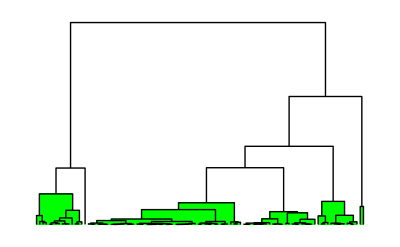

```mathematica
NCL=Range[1,n];
F0=MapThread[#1->#2&,{F,NCL}];
clastering =Agglomerate[F0,Linkage->"Ward"];
DendrogramPlot[clastering,HighlightLevel->6]
```

### Выберем оптимальное разбиение совокупности объектов на кластеры

```mathematica
Needs["ANOVA`"]
```

```mathematica
optimal=18;
```

```mathematica
Q=ClusterSplit[clastering,optimal][[2]]
```

Cluster[31,Cluster[73,61,1.87086,1,1],3.02885,1,2]

```mathematica
ClusterFlatten[Q]
```

{31,73,61}

```mathematica
Q=ClusterSplit[clastering,optimal];
Q1=Table[If[IntegerQ[Q[[i]]],{Q[[i]]},Sort[ClusterFlatten[Q[[i]]]]],{i,1,optimal}]
```

{{1},{31,61,73},{5,10,47,76,80,86,99},{18},{36,72,79},{51},{2,6,7,8,12,17,19,20,21,23,24,25,27,29,37,38,40,41,45,52,62,64,74,77,78,81,82,83,89,92,93,96,97,101},{3,15,34,35,44,65,66,70,84,88},{16,43,67,85},{4,11,28,33,39,46,49,59,68,69,90,95,102},{13,94},{14,22,26,48,54,55,75,91},{100},{30,63,87},{9,53,56,71,98},{42,57,58,60},{32},{50}}

```mathematica
numberingOfElements=ConstantArray[0,n];
For[i=1,i≤optimal,i++,
For[j=1,j≤Length[Q1[[i]]],j++,
numberingOfElements[[Q1[[i,j]]]]=i
]
];
numberingOfElements
```

{1,7,8,10,3,7,7,7,15,3,10,7,11,12,8,9,7,4,7,7,7,12,7,7,7,12,7,10,7,14,2,17,10,8,8,5,7,7,10,7,7,16,9,8,7,10,3,12,10,18,6,7,15,12,12,15,16,16,10,16,2,7,14,7,8,8,9,10,10,8,15,5,2,7,12,3,7,7,5,3,7,7,7,8,9,3,14,8,7,10,12,7,7,11,10,7,7,15,3,13,7,10}

```mathematica
FZ1=MapThread[{#1,#2}&,{numberingOfElements,F[[All,1]]}];
FZ2=MapThread[{#1,#2}&,{numberingOfElements,F[[All,2]]}];
FZ3=MapThread[{#1,#2}&,{numberingOfElements,F[[All,3]]}];
FZ4=MapThread[{#1,#2}&,{numberingOfElements,F[[All,4]]}];
```

```mathematica
ans1 = ANOVA[FZ1,PostTests->Bonferroni,CellMeans->False];
ans2 = ANOVA[FZ2,PostTests->Bonferroni,CellMeans->False];
ans3 = ANOVA[FZ3,PostTests->Bonferroni,CellMeans->False];
ans4 = ANOVA[FZ4,PostTests->Bonferroni,CellMeans->False];
ans1[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 325.478 | 19.1457 | 70.3284 | 2.78402×10^-42
Error | 84 | 22.8676 | 0.272234 |  | 
Total | 101 | 348.345 |  |  |

```mathematica
pValue1=ans1[[1,2]][[1,1,5]];
ans2[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 190.933 | 11.2314 | 58.6798 | 2.95366×10^-39
Error | 84 | 16.0777 | 0.191401 |  | 
Total | 101 | 207.011 |  |  |

```mathematica
pValue2=ans2[[1,2]][[1,1,5]];
ans3[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 117.284 | 6.89903 | 27.9127 | 1.83878×10^-27
Error | 84 | 20.7618 | 0.247164 |  | 
Total | 101 | 138.045 |  |  |

```mathematica
pValue3=ans3[[1,2]][[1,1,5]];
ans4[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 83.6423 | 4.92014 | 20.0735 | 1.13883×10^-22
Error | 84 | 20.5889 | 0.245106 |  | 
Total | 101 | 104.231 |  |  |

```mathematica
pValue4=ans4[[1,2]][[1,1,5]];
pValue={pValue1,pValue2,pValue3,pValue4}
```

{2.78402×10^-42,2.95366×10^-39,1.83878×10^-27,1.13883×10^-22}

```mathematica
list1=ans1[[2,2]][[1,2]]
a1=list1[[1,1,2]];
list2=ans2[[2,2]][[1,2]]
a2=list2[[1,1,2]];
list3=ans3[[2,2]][[1,2]]
a3=list3[[1,1,2]];
list4=ans4[[2,2]][[1,2]]
a4=list4[[1,1,2]];
list=Sort[DeleteDuplicates[Join[a1,a2,a3,a4]]]
```

Bonferroni | {{1,5},{3,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11},{2,12},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{9,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{11,13},{12,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{11,15},{12,15},{14,15},{2,16},{4,16},{5,16},{6,16},{7,16},{8,16},{9,16},{10,16},{13,16},{14,16},{15,16},{1,17},{2,17},{3,17},{4,17},{5,17},{6,17},{11,17},{12,17},{16,17},{2,18},{3,18},{4,18},{5,18},{6,18}}

Bonferroni | {{1,4},{2,4},{3,4},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{4,7},{6,7},{1,8},{2,8},{3,8},{5,8},{6,8},{7,8},{4,9},{6,9},{8,9},{4,10},{6,10},{7,10},{8,10},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11},{4,12},{6,12},{8,12},{11,12},{6,13},{11,13},{6,14},{10,14},{11,14},{4,15},{6,15},{11,15},{1,16},{2,16},{3,16},{5,16},{6,16},{7,16},{9,16},{10,16},{11,16},{12,16},{1,17},{2,17},{3,17},{4,17},{5,17},{7,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{15,17},{16,17},{1,18},{2,18},{3,18},{4,18},{5,18},{6,18},{7,18},{8,18},{9,18},{10,18},{11,18},{12,18},{13,18},{14,18},{15,18},{16,18},{17,18}}

Bonferroni | {{1,2},{1,5},{3,5},{1,6},{1,7},{5,7},{1,8},{5,8},{5,9},{5,10},{7,10},{2,11},{5,11},{6,11},{7,11},{8,11},{1,12},{10,12},{11,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{1,14},{2,14},{3,14},{4,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{1,16},{2,16},{3,16},{4,16},{7,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{13,17},{14,17},{15,17},{16,17},{2,18},{3,18},{5,18},{6,18},{7,18},{8,18},{9,18},{10,18},{12,18},{13,18},{14,18},{15,18},{16,18}}

Bonferroni | {{1,2},{1,3},{2,3},{1,4},{2,4},{1,5},{2,5},{1,6},{2,6},{1,7},{2,7},{1,8},{2,8},{1,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{9,10},{1,11},{2,11},{5,11},{7,11},{8,11},{9,11},{1,12},{2,12},{7,12},{8,12},{9,12},{1,13},{2,13},{9,13},{1,14},{9,14},{11,14},{12,14},{1,15},{2,15},{9,15},{11,15},{12,15},{1,16},{2,16},{9,16},{11,16},{12,16},{3,17},{4,17},{7,17},{10,17},{11,17},{12,17},{1,18},{2,18},{9,18},{14,18},{17,18}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{13,14},{13,15},{13,16},{13,17},{13,18},{14,15},{14,16},{14,17},{14,18},{15,16},{15,17},{15,18},{16,17},{16,18},{17,18}}

```mathematica
okey = True;
```

```mathematica
If[Sum[If[pValue[[i]]<0.05,0,1],{i,1,m}]==0,{Print["По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"]},{Print["Не по каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"],okey=False;}];
```

По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются

```mathematica
If[Length[list]==Sum[i,{i,1,optimal-1}],{Print["Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора"]},{Print["Для ",Abs[Length[list]-Sum[i,{i,1,optimal-1}] ]," пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора"],okey=False;}];
```

Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора

Таким образом, оптимальное количество кластеров равно 18. Для нахождения оптимального значения числа разбиений был организован перебор от optimal = 6 до optimal =18.

```mathematica
optimal=19;
```

```mathematica
ClusterSplit[clastering,optimal];
```

```mathematica
Q=ClusterSplit[clastering,optimal];
Q1=Table[If[IntegerQ[Q[[i]]],{Q[[i]]},Sort[ClusterFlatten[Q[[i]]]]],{i,1,optimal}]
```

{{1},{31,61,73},{5,10,47,76,80,86,99},{18},{36,72,79},{51},{2,6,7,8,12,17,19,20,21,23,24,25,27,29,37,38,40,41,45,52,62,64,74,77,78,81,82,83,89,92,93,96,97,101},{3,15,34,35,44,65,66,70,84,88},{16,43,67,85},{4,11,28,39,46,49,59,69,95},{33,68,90,102},{13,94},{14,22,26,48,54,55,75,91},{100},{30,63,87},{9,53,56,71,98},{42,57,58,60},{32},{50}}

```mathematica
numberingOfElements=ConstantArray[0,n];
For[i=1,i≤optimal,i++,
For[j=1,j≤Length[Q1[[i]]],j++,
numberingOfElements[[Q1[[i,j]]]]=i
]
];
numberingOfElements
```

{1,7,8,10,3,7,7,7,16,3,10,7,12,13,8,9,7,4,7,7,7,13,7,7,7,13,7,10,7,15,2,18,11,8,8,5,7,7,10,7,7,17,9,8,7,10,3,13,10,19,6,7,16,13,13,16,17,17,10,17,2,7,15,7,8,8,9,11,10,8,16,5,2,7,13,3,7,7,5,3,7,7,7,8,9,3,15,8,7,11,13,7,7,12,10,7,7,16,3,14,7,11}

```mathematica
FZ1=MapThread[{#1,#2}&,{numberingOfElements,F[[All,1]]}];
FZ2=MapThread[{#1,#2}&,{numberingOfElements,F[[All,2]]}];
FZ3=MapThread[{#1,#2}&,{numberingOfElements,F[[All,3]]}];
FZ4=MapThread[{#1,#2}&,{numberingOfElements,F[[All,4]]}];
```

```mathematica
ans1 = ANOVA[FZ1,PostTests->Bonferroni,CellMeans->False];
ans2 = ANOVA[FZ2,PostTests->Bonferroni,CellMeans->False];
ans3 = ANOVA[FZ3,PostTests->Bonferroni,CellMeans->False];
ans4 = ANOVA[FZ4,PostTests->Bonferroni,CellMeans->False];
ans1[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 18 | 328.297 | 18.2387 | 75.508 | 1.08188×10^-43
Error | 83 | 20.0484 | 0.241547 |  | 
Total | 101 | 348.345 |  |  |

```mathematica
pValue1=ans1[[1,2]][[1,1,5]];
ans2[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 18 | 190.98 | 10.61 | 54.9346 | 2.04521×10^-38
Error | 83 | 16.0306 | 0.193139 |  | 
Total | 101 | 207.011 |  |  |

```mathematica
pValue2=ans2[[1,2]][[1,1,5]];
ans3[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 18 | 117.393 | 6.52185 | 26.2112 | 8.01226×10^-27
Error | 83 | 20.652 | 0.248819 |  | 
Total | 101 | 138.045 |  |  |

```mathematica
pValue3=ans3[[1,2]][[1,1,5]];
ans4[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 18 | 86.4321 | 4.80178 | 22.3914 | 1.59716×10^-24
Error | 83 | 17.7991 | 0.214447 |  | 
Total | 101 | 104.231 |  |  |

```mathematica
pValue4=ans4[[1,2]][[1,1,5]];
pValue={pValue1,pValue2,pValue3,pValue4}
```

{1.08188×10^-43,2.04521×10^-38,8.01226×10^-27,1.59716×10^-24}

```mathematica
list1=ans1[[2,2]][[1,2]]
a1=list1[[1,1,2]];
list2=ans2[[2,2]][[1,2]]
a2=list2[[1,1,2]];
list3=ans3[[2,2]][[1,2]]
a3=list3[[1,1,2]];
list4=ans4[[2,2]][[1,2]]
a4=list4[[1,1,2]];
list=Sort[DeleteDuplicates[Join[a1,a2,a3,a4]]]
```

Bonferroni | {{1,5},{3,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{2,11},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{5,12},{6,12},{7,12},{8,12},{9,12},{10,12},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{1,16},{2,16},{3,16},{4,16},{5,16},{6,16},{11,16},{12,16},{13,16},{15,16},{2,17},{4,17},{5,17},{6,17},{7,17},{8,17},{9,17},{10,17},{14,17},{15,17},{16,17},{1,18},{2,18},{3,18},{4,18},{5,18},{6,18},{11,18},{12,18},{13,18},{17,18},{2,19},{3,19},{4,19},{5,19},{6,19},{12,19}}

Bonferroni | {{1,4},{2,4},{3,4},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{4,7},{6,7},{1,8},{2,8},{3,8},{5,8},{6,8},{7,8},{4,9},{6,9},{8,9},{4,10},{6,10},{7,10},{8,10},{4,11},{6,11},{8,11},{3,12},{4,12},{5,12},{6,12},{7,12},{8,12},{9,12},{4,13},{6,13},{8,13},{12,13},{6,14},{12,14},{6,15},{10,15},{12,15},{4,16},{6,16},{12,16},{1,17},{2,17},{3,17},{5,17},{6,17},{7,17},{9,17},{10,17},{11,17},{12,17},{13,17},{1,18},{2,18},{3,18},{4,18},{5,18},{7,18},{8,18},{9,18},{10,18},{11,18},{12,18},{13,18},{14,18},{15,18},{16,18},{17,18},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{11,19},{12,19},{13,19},{14,19},{15,19},{16,19},{17,19},{18,19}}

Bonferroni | {{1,2},{1,5},{3,5},{1,6},{1,7},{5,7},{1,8},{5,8},{5,9},{5,10},{7,10},{5,11},{2,12},{5,12},{6,12},{7,12},{8,12},{1,13},{10,13},{12,13},{1,14},{2,14},{3,14},{4,14},{5,14},{6,14},{7,14},{8,14},{9,14},{10,14},{11,14},{12,14},{13,14},{1,15},{2,15},{3,15},{4,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{1,16},{2,16},{3,16},{4,16},{7,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16},{1,17},{2,17},{3,17},{4,17},{7,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{14,18},{15,18},{16,18},{17,18},{2,19},{3,19},{5,19},{6,19},{7,19},{8,19},{10,19},{11,19},{13,19},{14,19},{15,19},{16,19},{17,19}}

Bonferroni | {{1,2},{1,3},{2,3},{1,4},{2,4},{1,5},{2,5},{1,6},{2,6},{1,7},{2,7},{1,8},{2,8},{1,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{8,10},{9,10},{1,11},{2,11},{9,11},{1,12},{2,12},{5,12},{7,12},{8,12},{9,12},{11,12},{1,13},{2,13},{7,13},{8,13},{9,13},{11,13},{1,14},{2,14},{9,14},{1,15},{2,15},{4,15},{9,15},{10,15},{12,15},{13,15},{1,16},{2,16},{9,16},{12,16},{13,16},{1,17},{2,17},{9,17},{12,17},{13,17},{1,18},{3,18},{4,18},{7,18},{10,18},{12,18},{13,18},{1,19},{2,19},{9,19},{15,19},{18,19}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{14,15},{14,16},{14,17},{14,18},{14,19},{15,16},{15,17},{15,18},{15,19},{16,17},{16,18},{16,19},{17,18},{17,19},{18,19}}

```mathematica
okey = True;
```

```mathematica
If[Sum[If[pValue[[i]]<0.05,0,1],{i,1,m}]==0,{Print["По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"]},{Print["Не по каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"],okey=False;}];
```

По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются

```mathematica
If[Length[list]==Sum[i,{i,1,optimal-1}],{Print["Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора"]},{Print["Для ",Abs[Length[list]-Sum[i,{i,1,optimal-1}] ]," пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора"],okey=False;}];
```

Для 1 пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора

Видим, что при разбиении на 19 кластеров нет значимого различия средних хотя бы для одного фактора

### Проведем кластеризацию методом k-средних, количество кластеров возьмем равным q = 18 - значение, которое является оптимальным для предыдущего метода.

```mathematica
optimal=18;
```

```mathematica
CL=FindClusters[F0,optimal,Method->"KMeans", DistanceFunction->EuclideanDistance]
```

{{1,16},{2,3,12,17,21,23,29,37,41,52,64,65,82,97},{4,11,28,39,46,49,59,95},{5,31,47,61,73,79},{6,7,8,78,92,96},{9,20,53,56,71,98},{10,13,94},{14,22,33,48,54,55,68,75,80,90,91,102},{15,35,44,70,84,88,93},{18,26,36,72,76,86,99},{19,24,25,27,38,40,45,62,74,77,81,83,89,101},{30,63,87},{32,50},{34,43,66,67,85},{42,57,58,60},{51},{69},{100}}

{{1},{31,61,73},{5,10,47,76,80,86,99},{18},{36,72,79},{51},{2,6,7,8,12,17,19,20,21,23,24,25,27,29,37,38,40,41,45,52,62,64,74,77,78,81,82,83,89,92,93,96,97,101},{3,15,34,35,44,65,66,70,84,88},{16,43,67,85},{4,11,28,39,46,49,59,69,95},{33,68,90,102},{13,94},{14,22,26,48,54,55,75,91},{100},{30,63,87},{9,53,56,71,98},{42,57,58,60},{32},{50}}

```mathematica
numberingOfElements=ConstantArray[0,n];
For[i=1,i≤optimal,i++,
For[j=1,j≤Length[CL[[i]]],j++,
numberingOfElements[[CL[[i,j]]]]=i]]
numberingOfElements
```

{1,2,2,3,4,5,5,5,6,7,3,2,7,8,9,1,2,10,11,6,2,8,2,11,11,10,11,3,2,12,4,13,8,14,9,10,2,11,3,11,2,15,14,9,11,3,4,8,3,13,16,2,6,8,8,6,15,15,3,15,4,11,12,2,2,14,14,8,17,9,6,10,4,11,8,10,11,5,4,8,11,2,11,9,14,10,12,9,11,8,8,5,9,7,3,5,2,6,10,18,11,8}

```mathematica
FZ11=MapThread[{#1,#2}&,{numberingOfElements,F[[All,1]]}];
FZ21=MapThread[{#1,#2}&,{numberingOfElements,F[[All,2]]}];
FZ31=MapThread[{#1,#2}&,{numberingOfElements,F[[All,3]]}];
FZ41=MapThread[{#1,#2}&,{numberingOfElements,F[[All,4]]}];
```

```mathematica
km1 = ANOVA[FZ11,PostTests->Bonferroni,CellMeans->False];
km2 = ANOVA[FZ21,PostTests->Bonferroni,CellMeans->False];
km3 = ANOVA[FZ31,PostTests->Bonferroni,CellMeans->False];
km4 = ANOVA[FZ41,PostTests->Bonferroni,CellMeans->False];
```

```mathematica
km1[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 321.905 | 18.9356 | 60.1577 | 1.14171×10^-39
Error | 84 | 26.4403 | 0.314766 |  | 
Total | 101 | 348.345 |  |  |

```mathematica
pValue1=km1[[1,2]][[1,1,5]];
km2[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 177.931 | 10.4665 | 30.2333 | 1.1386×10^-28
Error | 84 | 29.0801 | 0.346192 |  | 
Total | 101 | 207.011 |  |  |

```mathematica
pValue2=km2[[1,2]][[1,1,5]];
km3[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 118.566 | 6.9745 | 30.0765 | 1.3663×10^-28
Error | 84 | 19.4789 | 0.231892 |  | 
Total | 101 | 138.045 |  |  |

```mathematica
pValue3=km3[[1,2]][[1,1,5]];
km4[[1,2]]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 17 | 71.1126 | 4.18309 | 10.6097 | 1.64316×10^-14
Error | 84 | 33.1187 | 0.39427 |  | 
Total | 101 | 104.231 |  |  |

```mathematica
pValue4=km4[[1,2]][[1,1,5]];
kmpValue={pValue1,pValue2,pValue3,pValue4}
```

{1.14171×10^-39,1.1386×10^-28,1.3663×10^-28,1.64316×10^-14}

```mathematica
list1=km1[[2,2]][[1,2]]
a1=list1[[1,1,2]];
list2=km2[[2,2]][[1,2]]
a2=list2[[1,1,2]];
list3=km3[[2,2]][[1,2]]
a3=list3[[1,1,2]];
list4=km4[[2,2]][[1,2]]
a4=list4[[1,1,2]];
kmlist=Sort[DeleteDuplicates[Join[a1,a2,a3,a4]]]
```

Bonferroni | {{1,4},{2,4},{3,4},{1,5},{3,5},{4,5},{4,6},{2,7},{3,7},{5,7},{6,7},{2,8},{3,8},{4,8},{5,8},{6,8},{4,9},{7,9},{8,9},{1,10},{2,10},{3,10},{5,10},{6,10},{8,10},{9,10},{1,11},{2,11},{3,11},{4,11},{7,11},{8,11},{10,11},{1,12},{2,12},{3,12},{4,12},{6,12},{7,12},{8,12},{9,12},{10,12},{4,13},{7,13},{8,13},{10,13},{4,14},{7,14},{8,14},{10,14},{11,14},{12,14},{2,15},{3,15},{4,15},{5,15},{6,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{1,16},{2,16},{3,16},{4,16},{5,16},{6,16},{7,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16},{15,16},{4,17},{10,17},{16,17},{4,18},{7,18},{8,18},{10,18},{15,18},{16,18}}

Bonferroni | {{2,7},{6,7},{1,9},{2,9},{3,9},{4,9},{5,9},{7,9},{8,9},{7,10},{7,11},{9,11},{7,12},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{7,14},{13,14},{1,15},{3,15},{4,15},{7,15},{8,15},{13,15},{1,16},{2,16},{3,16},{4,16},{5,16},{6,16},{7,16},{8,16},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16},{15,16},{9,17},{13,17},{15,17},{16,17},{13,18},{16,18}}

Bonferroni | {{1,2},{1,4},{1,5},{3,5},{1,6},{2,6},{3,6},{4,6},{5,6},{2,7},{4,7},{5,7},{6,7},{1,8},{6,8},{7,8},{1,9},{6,9},{1,10},{3,10},{7,10},{8,10},{9,10},{1,11},{5,11},{6,11},{10,11},{1,12},{2,12},{3,12},{4,12},{5,12},{7,12},{8,12},{9,12},{10,12},{11,12},{2,13},{4,13},{5,13},{6,13},{8,13},{9,13},{10,13},{11,13},{12,13},{6,14},{10,14},{12,14},{1,15},{2,15},{3,15},{4,15},{5,15},{7,15},{8,15},{9,15},{10,15},{11,15},{13,15},{14,15},{1,16},{7,16},{13,16},{5,17},{6,17},{10,17},{12,17},{15,17},{1,18},{2,18},{3,18},{4,18},{5,18},{6,18},{7,18},{8,18},{9,18},{10,18},{11,18},{12,18},{13,18},{14,18},{15,18},{16,18},{17,18}}

Bonferroni | {{1,2},{1,3},{1,4},{2,4},{3,4},{1,5},{4,5},{1,6},{1,7},{4,7},{1,8},{4,8},{1,9},{1,10},{4,10},{1,11},{4,11},{1,12},{7,12},{1,13},{1,14},{2,14},{3,14},{5,14},{7,14},{8,14},{9,14},{10,14},{11,14},{1,15},{1,16},{1,17},{4,17},{14,17},{1,18}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{2,4},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,18},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,18},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,18},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,18},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{11,12},{11,13},{11,14},{11,15},{11,16},{11,18},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{13,14},{13,15},{13,16},{13,17},{13,18},{14,15},{14,16},{14,17},{14,18},{15,16},{15,17},{15,18},{16,17},{16,18},{17,18}}

```mathematica
okey=True;
```

```mathematica
If[Sum[If[kmpValue[[i]]<0.05,0,1],{i,1,m}]==0,{Print["По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"]},{Print["Не по каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются"],okey=False;}];
```

По каждому фактору средние значения фактора по кластерам для всей совокупности кластеров значимо различаются

```mathematica
If[Length[kmlist]==Sum[i,{i,1,optimal-1}],{Print["Для каждой пары различных кластеров существует значимое различие средних хотя бы для одного фактора"]},{Print["Для ",Abs[Length[kmlist]-Sum[i,{i,1,optimal-1}] ]," пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора"],okey=False;}];
```

Для 7 пар(ы) различных кластеров нет значимого различия средних хотя бы для одного фактора

### Сравним два полученных разбиения

```mathematica
FW1=Table[F[[Q1[[i]]]],{i,1,optimal}];
FW2=Table[F[[CL[[i]]]],{i,1,optimal}];
```

```mathematica
FW1means=Table[Mean[FW1[[i]]],{i,1,optimal}]
FW2means=Table[Mean[FW2[[i]]],{i,1,optimal}]
```

{{-1.69323,0.947759,2.26692,4.4778},{-2.96022,0.793413,-0.0976522,2.25493},{-2.27011,0.357853,0.413766,-0.345828},{-3.52951,-1.87022,0.500262,-1.36418},{-4.37962,0.552283,-1.1081,0.0173691},{-9.10726,-4.26186,-0.859973,-0.0129076},{1.29611,0.228484,0.158632,-0.159151},{0.508113,-0.858668,0.214346,0.238795},{0.589889,0.477406,0.862334,2.17827},{0.0246304,0.825337,0.88341,-0.380875},{-1.73935,2.07133,1.69483,-1.69347},{-0.82153,0.501797,-0.246305,-1.10328},{1.82312,-0.505436,-5.36703,-0.377962},{2.69505,-0.517318,-2.27814,0.758692},{0.616206,-0.012725,-1.64127,0.222292},{-1.14999,-0.925669,-2.13019,0.111539},{1.42777,-5.47907,0.88596,1.92917},{0.645385,-10.0328,2.96643,-1.40708}}

{{-0.481517,1.02884,1.96031,3.80088},{0.715473,0.280056,0.0832535,-0.0722177},{0.324207,0.759681,0.863776,-0.609562},{-3.21789,0.731215,0.122517,1.27041},{1.64815,0.255623,-0.418056,-0.391785},{0.704801,0.0513527,-1.5374,0.186081},{-1.93369,1.72954,1.51147,-1.44328},{-0.742351,0.529502,0.293267,-0.498424},{0.718004,-1.06519,0.349559,0.0114405},{-2.88138,-0.0229874,-0.658285,-0.748114},{1.59686,0.14192,0.488609,-0.117038},{2.69505,-0.517318,-2.27814,0.758692},{1.03658,-7.75593,1.9262,0.261044},{0.468595,-0.0750626,0.481202,1.49622},{-1.14999,-0.925669,-2.13019,0.111539},{-9.10726,-4.26186,-0.859973,-0.0129076},{0.422129,1.71177,1.59199,-1.33086},{1.82312,-0.505436,-5.36703,-0.377962}}

Сумма средних квадратов расстояния до центров кластеров для разбиения, полученного с помощью метода Варда:

```mathematica
FW1MS=Sum[Mean[Table[Norm[(FW1[[j,i]]-FW1means[[j]])^2],{i,1,Length[FW1[[j]]]}]],{j,1,optimal}]
```

7.71153

Сумма средних квадратов расстояния до центров кластеров для разбиения, полученного методом k-средних:

```mathematica
FW2MS=Sum[Mean[Table[Norm[(FW2[[j,i]]-FW2means[[j]])^2],{i,1,Length[FW2[[j]]]}]],{j,1,optimal}]
```

16.4647

## Вывод :

В среднем квадрат расстояния до центра кластера при кластеризации методом k - средних получился значительно больше, чем та же метрика при кластеризации с использованием алгоритма Варда . Следовательно Метод Варда более точно разделяет наблюдения на кластеры в смысле метрики заданной выше .